```mathematica
Get["http://www.fmt.if.usp.br/~gtlandi/download/melt.m"]
```

```mathematica
UnconditionalDynamicsXX[γ_,T_,Δt_,δ_,nCol_]:=Module[{ω,Ν,g,ρA,gDown,gUp,H0NonMarkovian,HIdownNonMarkovian,HIupNonMarkovian,U,UAADown,UAAUp,USB,ρSS ,UnconditionalStates},
ω=1;
Ν=1/(Exp[ω/T]-1);
g=1/(2Ν + 1);
ρA= kron[out[Basis[2,2],Basis[2,2]],out[Basis[2,1],Basis[2,1]]];
gDown=Sqrt[γ (Ν+1)];
gUp=Sqrt[γ (Ν)];

H0NonMarkovian=kron[σz/2,σz/2,σz/2,σz/2,σz/2];
HIdownNonMarkovian = -(1/2)(1/Sqrt[Δt])gDown (KronEye[σx,5,1].KronEye[σx,5,2]+KronEye[σy,5,1].KronEye[σy,5,2]);
HIupNonMarkovian = -(1/2)(1/Sqrt[Δt]) gUp(KronEye[σx,5,1].KronEye[σx,5,3]+KronEye[σy,5,1].KronEye[σy,5,3]);

U =MatrixExp[-ⅈ (H0NonMarkovian+HIdownNonMarkovian+HIupNonMarkovian)Δt];
UAADown = PartialSWAP[δ,2,4,5];
UAAUp = PartialSWAP[δ,3,5,5];
USB=UAAUp.UAADown.U;

ρSS = PTr[CollisionModelSteadyState[UAAUp.SWAP[3,5,5].UAADown.SWAP[2,4,5].U,ρA],{2,3}];
UnconditionalStates=ParallelTable[PTr[CollisionMap[kron[out[Basis[2,2],Basis[2,2]],ρA],UAAUp.SWAP[3,5,5].UAADown.SWAP[2,4,5].U,ρA,nCol][[i]],{2,3}],{i,1,nCol}]//Chop
]
UNonMarkovianfunctionXX[γ_,T_,Δt_,δ_]:= Module[{Ν,gDown,gUp,H0NonMarkovian,HIdownNonMarkovian,ω,HIupNonMarkovian,UAA,USATotalNonMarkovian},
ω=1;
Ν=1/(Exp[ω/T]-1);
gDown=Sqrt[γ (Ν+1)];
gUp=Sqrt[γ (Ν)];
H0NonMarkovian=kron[σz/2,σz/2,σz/2,σz/2,σz/2];
HIdownNonMarkovian = -(1/2)(1/Sqrt[Δt])gDown (KronEye[σx,5,1].KronEye[σx,5,2]+KronEye[σy,5,1].KronEye[σy,5,2]);
HIupNonMarkovian = -(1/2)(1/Sqrt[Δt])gUp (KronEye[σx,5,1].KronEye[σx,5,3]+KronEye[σy,5,1].KronEye[σy,5,3]);
UAA = PartialSWAP[δ,3,5,5].SWAP[3,5,5].PartialSWAP[δ,2,4,5].SWAP[2,4,5];
USATotalNonMarkovian = UAA.MatrixExp[-ⅈ (H0NonMarkovian+HIdownNonMarkovian+HIupNonMarkovian)Δt]
]
```

```mathematica
NonMarkovianTrajectorySSXX[γ_,T_,Δt_,δ_,nCol_]:=Module[{ρS0,Ν,ω,gDown,gUp,H0NonMarkovian,HIdownNonMarkovian,HIupNonMarkovian,U,HAnc,energyBefore,energyAfter,g,ρA,
SBstateAfterFirst,(*Intermediate system-bath state after first collision*)
SBstateAfterCollision,
SBstateAfterSecond,(*Intermediate system-bath state after second collision*)
SBstateBeforeFirst,(*System-bath state before any collision*)
ReducedState={},(*List to store reduced system states*)
HIdown,HIup,(*Interaction Hamiltonians*)
USATotal,(*Unitary evolution operator for system-ancillas*)
UAADown,UAAUp,(*Partial swap operations*)
USB,(*Total unitary operation for system and baths*)
ρS,(*Reduced density matrix of the system*)
P0,P1,(*Projectors for the ancilla states*)
P0η1,P1η1,(*Projectors applied to first ancilla*)
P0η2,P1η2,(*Projectors applied to second ancilla*)
p0η1,p1η1,(*Probabilities for first ancilla*)
p0η2,p1η2,(*Probabilities for second ancilla*)
A0StochasticHeat,A0StochasticHeatList={},
FirstProb0,FirstProb1,SecondProb0,SecondProb1,Prob0,Prob1,SBstateAfterThird,SBstateAfterFourth,
FirstProb0List={},
ExpandedState
},
P0=out[Basis[2,2],Basis[2,2]];
P1=out[Basis[2,1],Basis[2,1]];
(*Projectors on the extended space*)
P0η1=KronEye[P0,5,2];
P1η1=KronEye[P1,5,2];
P0η2 =KronEye[P0,5,3];
P1η2 =KronEye[P1,5,3];

ω=1;
Ν=1/(Exp[ω/T]-1);
g=1/(2Ν + 1);
ρA= kron[out[Basis[2,2],Basis[2,2]],out[Basis[2,1],Basis[2,1]]];
gDown=Sqrt[γ (Ν+1)];
gUp=Sqrt[γ (Ν)];

H0NonMarkovian=kron[σz/2,σz/2,σz/2,σz/2,σz/2];
HIdownNonMarkovian = -(1/2)(1/Sqrt[Δt])gDown (KronEye[σx,5,1].KronEye[σx,5,2]+KronEye[σy,5,1].KronEye[σy,5,2]);
HIupNonMarkovian = -(1/2)(1/Sqrt[Δt]) gUp(KronEye[σx,5,1].KronEye[σx,5,3]+KronEye[σy,5,1].KronEye[σy,5,3]);

U =MatrixExp[-ⅈ (H0NonMarkovian+HIdownNonMarkovian+HIupNonMarkovian)Δt];
UAADown = PartialSWAP[δ,2,4,5];
UAAUp = PartialSWAP[δ,3,5,5];
USB=UAAUp.UAADown.U;

ρS0 =out[Basis[2,2],Basis[2,2]];
(*PTr[CollisionModelSteadyState[SWAP[3,5,5].UAAUp.SWAP[2,4,5].UAADown.U,ρA],{2,3}];
*)


(*Main loop over the number of collisions*)
ExpandedState[0]=DM[kron[ρS0,ρA,ρA]];
Do[

SBstateBeforeFirst[i] = DM[Chop[ExpandedState[i-1]]];


(*Do the Collision Unitaries*)
SBstateAfterCollision[i]=DM[Chop[USB.SBstateBeforeFirst[i].ConjugateTranspose[USB]]];

(*Do the second measurement in the TPM*)
SecondProb0=Chop[Tr[P0η1.SBstateAfterCollision[i].ConjugateTranspose[P0η1]]];
If[RandomReal[]<SecondProb0,
SBstateAfterFirst[i]=DM[P0η1.SBstateAfterCollision[i].ConjugateTranspose[P0η1]],
SBstateAfterFirst[i]=DM[P1η1.SBstateAfterCollision[i].ConjugateTranspose[P1η1]]
];

A0StochasticHeat[i] = Tr[(σz/2).(PTr[SBstateAfterFirst[i],{1,3,4,5}]-out[Basis[2,2],Basis[2,2]])];
AppendTo[A0StochasticHeatList,A0StochasticHeat[i]];

SecondProb1=Chop[Tr[P0η2.SBstateAfterFirst[i].ConjugateTranspose[P0η2]]];
If[RandomReal[]<SecondProb1,
SBstateAfterSecond[i]=DM[P0η2.SBstateAfterFirst[i].ConjugateTranspose[P0η2]],
SBstateAfterSecond[i]=DM[P1η2.SBstateAfterFirst[i].ConjugateTranspose[P1η2]]
];

ExpandedState[i] = kron[PTr[SBstateAfterSecond[i],{2,3}],ρA];
(*Compute reduced state of the system*)
(*ρS[i]=DM[PTr[SBstateAfterSecond[i],{2,3,4,5}]];
AppendTo[ReducedState,ρS[i]];*)
,{i,1,nCol}];(*End of Do loop*)

(*Return the reduced states and the list of jump events*)
(*{ReducedState,*)A0StochasticHeatList(*}*)]
UnconditionalHeatCurrentXX[γ_,T_,Δt_,δ_,nCol_]:=Module[{ω,Ν,g,ρA,gDown,gUp,H0NonMarkovian,HIdownNonMarkovian,HIupNonMarkovian,U,UAADown,UAAUp,USB,ρSS ,UnconditionalStates,ExpandedSystemStates,UnconditionalA0States,A0HeatCurrent,A0HeatList={} ,ρS0,ExpandedState,SBstateBeforeFirst,SBstateAfterCollision},
ω=1;
Ν=1/(Exp[ω/T]-1);
g=1/(2Ν + 1);
ρA= kron[out[Basis[2,2],Basis[2,2]],out[Basis[2,1],Basis[2,1]]];
gDown=Sqrt[γ (Ν+1)];
gUp=Sqrt[γ (Ν)];

H0NonMarkovian=kron[σz/2,σz/2,σz/2,σz/2,σz/2];
HIdownNonMarkovian = -(1/2)(1/Sqrt[Δt])gDown (KronEye[σx,5,1].KronEye[σx,5,2]+KronEye[σy,5,1].KronEye[σy,5,2]);
HIupNonMarkovian = -(1/2)(1/Sqrt[Δt]) gUp(KronEye[σx,5,1].KronEye[σx,5,3]+KronEye[σy,5,1].KronEye[σy,5,3]);

U =MatrixExp[-ⅈ (H0NonMarkovian+HIdownNonMarkovian+HIupNonMarkovian)Δt];
UAADown = PartialSWAP[δ,2,4,5];
UAAUp = PartialSWAP[δ,3,5,5];
USB=UAAUp.UAADown.U;

ρSS = PTr[CollisionModelSteadyState[UAAUp.SWAP[3,5,5].UAADown.SWAP[2,4,5].U,ρA],{2,3}];
ρS0 = out[Basis[2,2],Basis[2,2]];
(*Main loop over the number of collisions*)
ExpandedState[0]=DM[kron[ρS0,ρA,ρA]];
Do[

SBstateBeforeFirst[i] = DM[Chop[ExpandedState[i-1]]];


(*Do the Collision Unitaries*)
SBstateAfterCollision[i]=DM[Chop[USB.SBstateBeforeFirst[i].ConjugateTranspose[USB]]];

(*Do the second measurement in the TPM*)

A0HeatCurrent[i] = Tr[(σz/2).(PTr[SBstateAfterCollision[i],{1,3,4,5}]-out[Basis[2,2],Basis[2,2]])];
AppendTo[A0HeatList,A0HeatCurrent[i]];



ExpandedState[i] = kron[PTr[SBstateAfterCollision[i],{2,3}],ρA];
(*Compute reduced state of the system*)
,{i,1,nCol}];(*End of Do loop*)


A0HeatList

]
```

```mathematica
γXX = 4;
T=1;
Δt=0.0025;
ρA = kron[out[Basis[2,2],Basis[2,2]],out[Basis[2,1],Basis[2,1]]];
nCol=400;
nTraj=10000;
δ=0.95;
```

```mathematica
AllTrajectories10k=ParallelTable[NonMarkovianTrajectorySSXX[γXX,T,Δt,δ,nCol],10000];
AveragedTrajectories10K=Total[AllTrajectories10k]/10000;
```

```mathematica
AllTrajectories100k=ParallelTable[NonMarkovianTrajectorySSXX[γXX,T,Δt,δ,nCol],100000];
AveragedTrajectories100K=Total[AllTrajectories100k]/100000;
```

```mathematica
UnconditionalHeatcurrent=UnconditionalHeatCurrentXX[γXX,T,Δt,δ,nCol]//Chop;
```

```mathematica
UnconditionalDataXX = Table[{i*Δt,UnconditionalHeatcurrent[[i]]/Δt},{i,1,nCol}]//Chop;
TenKTrajectoriesDataXX = Table[{i*Δt,AveragedTrajectories10K[[i]]/Δt},{i,1,nCol}]//Chop;
OneHundredKTrajectoriesDataXX= Table[{i*Δt,AveragedTrajectories100K[[i]]/Δt},{i,1,nCol}]//Chop;
```

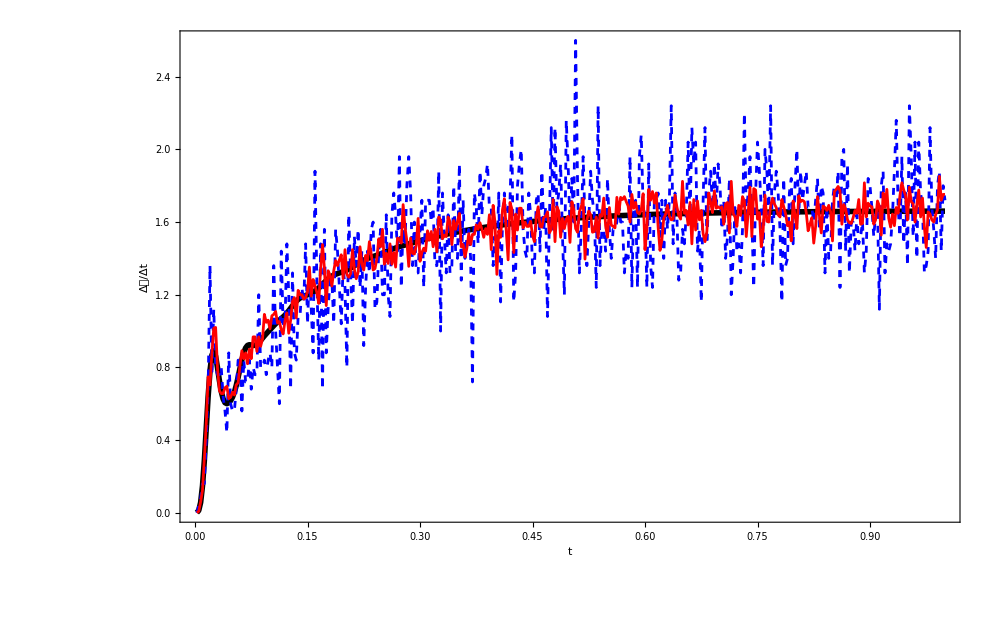

```mathematica
ListLinePlot[{UnconditionalDataXX,TenKTrajectoriesDataXX,OneHundredKTrajectoriesDataXX},Frame->True,
PlotStyle->{Directive[Darker[Black],Thickness[0.004]],Directive[Blue,Dashed](*RGBColor[55/255,126/255,184/255]*),Directive[Red](*Directive[RGBColor[228/255,26/255,28/255]]*),Directive[RGBColor[77/255,175/255,74/255]]},
(*Filling->{2->{3},2->{4},5->{6},5->{7},8->{9},8->{10}}*)
PlotRange->All,
LabelStyle->Directive[Black,FontFamily->"Times",40],
FrameLabel->{{"Δ𝒬/Δt",""},{"t",""}},
FrameStyle->Directive[Black,Thick],
(*PlotLegends->LineLegend[{Black,RGBColor[55/255,126/255,184/255],RGBColor[228/255,26/255,28/255],RGBColor[77/255,175/255,74/255]},{"Unconditional","10,000 Trajectories","100,000 Trajectories","300,000 Trajectories"}]*)
ImageSize->1000]
```